```mathematica
AbsoluteTiming [Plot[{9+(1)16-(1)(1-k)^2-(1)(k)^2,((3)k+4(1)(1-k))^2},{k,0,1},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},PlotStyle->{Yellow, Red},PlotStyle->Opacity[5],Axes->True,Filling->Axis,PlotLegends->Placed[{"R","L"},{0.1,0.1}]]]
```

```mathematica
{0.1657486,-Graphics-}
```

```mathematica
AbsoluteTiming [Plot3D[{a^2+(1)(b^2)-(1)((1-0.5)(b-a))^2-(1)((0.5)(b-a))^2,((a)(0.5)+(b)(1)(1-0.5))^2},{a,3,3.4},{b,3.5,4},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{Yellow, Red},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],Axes->True,PlotLegends->Placed[{"R","L"},{0.1,0.1}]]]
```

{2.70424,-Graphics-}

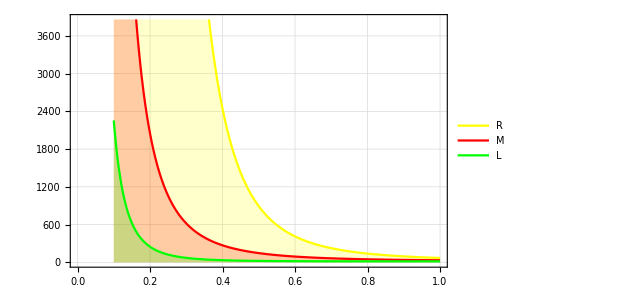
{4.95325,-Graphics-}

```mathematica
AbsoluteTiming [Plot[{2^3+m((3/m)^3+(2/m)^3+(3/(m^2))^3)-(Integrate[(((x-2)(3-2m))/m)^3+m((((3-x)(3-2m))/m)^3)+m((((3-x)(3-2m))/m^2)^3)+m^2((((x-2)(3-2m))/m^2)^3),{x,2,3}]),Integrate[(x)^3,{x,2,3}]+m(Integrate[(x)^3,{x,2/m,3/m}]),(5/2)^3+2(1+m)(Integrate[((5-(1+m)x)/(2m))^3,{x,2,5/2}])},{m,0.1,1},ImageSize -> {473., Automatic},PlotStyle->{Yellow, Red, Green},Mesh->None,Ticks->{Automatic,Automatic,Automatic},Frame->True,RotateLabel->False,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed], Background->Opacity[1,White], PlotRange ->Automatic,Filling->Axis,LabelStyle->{FontSize->13.5,Bold},Axes->True,PlotLegends->Placed[{"R","M","L"},{0.9,0.79}]]]
```

```mathematica
Table[2^3+m((3/m)^3+(2/m)^3+(3/(m^2))^3)-(Integrate[(((x-2)(3-2m))/m)^3+m((((3-x)(3-2m))/m)^3)+m((((3-x)(3-2m))/m^2)^3)+m^2((((x-2)(3-2m))/m^2)^3),{x,2,3}]),{m,0.1,1.0,0.1}]
```

{2.09379×10^6,68121.4,9492.71,2441.29,892.,411.644,224.643,138.905,94.4187,69.}

```mathematica
Table[Integrate[(x)^3,{x,2,3}]+m(Integrate[(x)^3,{x,2/m,3/m}]),{m,0.1,1.0,0.1}]
```

{16266.3,2047.5,618.102,270.156,146.25,91.4815,63.6261,47.9883,38.5408,32.5}

```mathematica
Table[(5/2)^3+2(1+m)(Integrate[((5-(1+m)x)/(2m))^3,{x,2,5/2}]),{m,0.1,1.0,0.1}]
```

{2255.42,247.638,70.7146,33.5577,22.4043,18.3731,16.7615,16.0863,15.8024,15.6875}